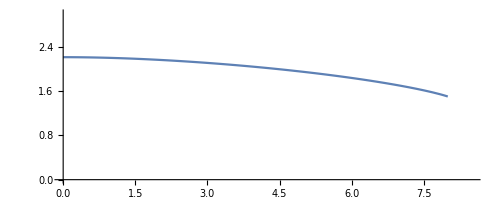

```mathematica
ν=0.03;
ϵ=0.002;
thickness=1.5;
radius=8;
start= 0.000000000001;

eq1=ρ/1 D[ρ((D[r2[ρ],ρ])+(ν r2[ρ])/1+1/2 ρ(D[z1[ρ], ρ])^2), ρ]-ν/1 ρ(D[r2[ρ],ρ]+1/2(D[z1[ρ], ρ])^2)-r2[ρ]/1==0;
eq2=1/1 D[1(D[z1[ρ], ρ])(D[r2[ρ],ρ]ρ+ν r2[ρ]/1+1/2(D[z1[ρ], ρ])^2 ρ), ρ]==-ρ;
s=NDSolve[{eq1, eq2, r2[1]==0,z1[1]==0,(D[z1[ρ], ρ]/.ρ->0)==0 , r2[start]==0},{r2, z1},{ρ,start,1}];
(*simplethickness plot*)
expr0 = {radius*(ρ+ϵ^(2/3) r2[ρ]),radius*(ϵ^(1/3)z1[ρ])+thickness};
ParametricPlot[{Evaluate[expr0/.s]}, {ρ, start, 1}, PlotRange->{{0, 8.5},{0, 3}}]


(*ParametricPlot[{Evaluate[{radius*(1+ϵ^(2/3)r2'[ρ]),radius*(ϵ^(1/3)z1'[ρ])}/.s]}, {ρ, start, 1}, PlotRange->Full]*)
(*ParametricPlot[Evaluate[r2[ρ], z1[ρ]]/.s, {ρ, 0.1, 1}]*)
```

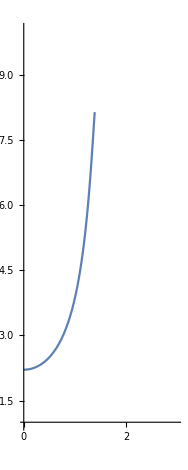

InterpolatingFunction::dmval: Input value {1.001} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

thickness.txt

```mathematica
(*thickness as a function of angle from normal*)
expr1 = {ArcTan[radius*(ρ+ϵ^(2/3) r2[ρ])/(radius*(ϵ^(1/3)z1[ρ])+thickness)],√((radius*(ρ+ϵ^(2/3) r2[ρ]))^2+(radius*(ϵ^(1/3)z1[ρ])+thickness)^2)};
ParametricPlot[{Evaluate[expr1/.s]}, {ρ, start, 1}, PlotRange->{{0, 3},{1,10 }}]
Export["thickness.txt",Table[Evaluate[expr1/.s], {ρ, start, 2.0, 0.001}]]
```

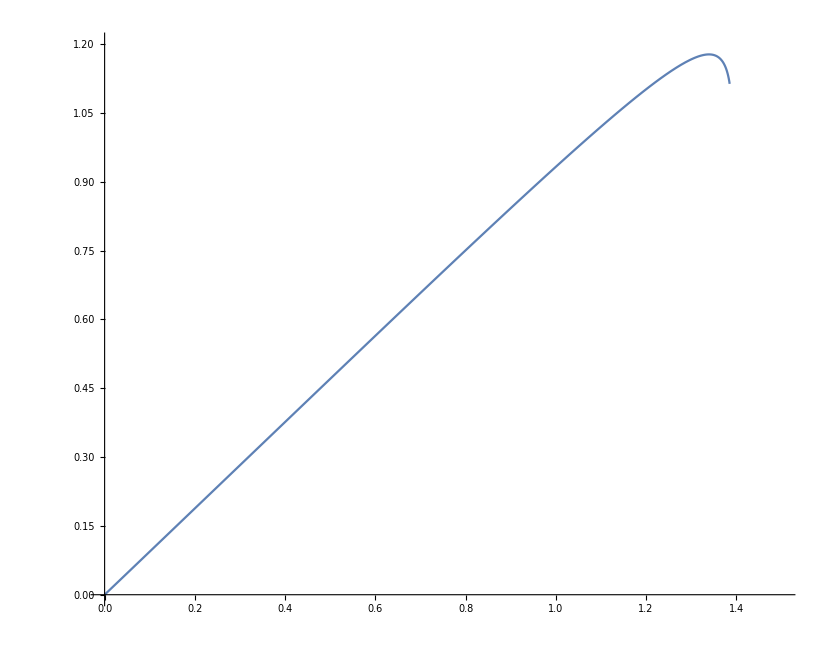

InterpolatingFunction::dmval: Input value {1.001} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{{{3.62129×10^-12,3.45679×10^-12}},{{0.00363625,0.00340584}},{{0.00727274,0.00681673}},{{0.0109092,0.0102293}},{{0.0145454,0.0136429}},{{0.0181814,0.0170571}},{{0.0218169,0.0204716}},{{0.025452,0.0238861}},{{0.0290865,0.0273006}},{{0.0327203,0.0307149}},{{0.0363534,0.0341289}},{{0.0399856,0.0375424}},{{0.0436169,0.0409553}},{{0.0472472,0.0443675}},{{0.0508763,0.0477789}},{{0.0545043,0.0511895}},{{0.0581309,0.0545991}},{{0.0617562,0.0580075}},{{0.06538,0.0614149}},{{0.0690023,0.0648209}},{{0.0726229,0.0682256}},{{0.0762418,0.0716288}},{{0.0798589,0.0750305}},{{0.0834741,0.0784306}},{{0.0870873,0.081829}},{{0.0906985,0.0852256}},{{0.0943075,0.0886203}},{{0.0979143,0.0920131}},{{0.101519,0.0954038}},{{0.105121,0.0987924}},{{0.10872,0.102179}},{{0.112317,0.105563}},{{0.115912,0.108945}},{{0.119503,0.112324}},{{0.123092,0.115701}},{{0.126678,0.119075}},{{0.130261,0.122446}},{{0.133841,0.125815}},{{0.137418,0.129181}},{{0.140991,0.132543}},{{0.144562,0.135903}},{{0.148129,0.13926}},{{0.151692,0.142614}},{{0.155252,0.145964}},{{0.158808,0.149311}},{{0.162361,0.152655}},{{0.16591,0.155995}},{{0.169455,0.159332}},{{0.172996,0.162665}},{{0.176533,0.165995}},{{0.180067,0.16932}},{{0.183596,0.172642}},{{0.18712,0.17596}},{{0.190641,0.179274}},{{0.194157,0.182584}},{{0.197669,0.18589}},{{0.201176,0.189192}},{{0.204679,0.19249}},{{0.208177,0.195783}},{{0.211671,0.199072}},{{0.215159,0.202356}},{{0.218643,0.205636}},{{0.222122,0.208911}},{{0.225596,0.212182}},{{0.229065,0.215448}},{{0.232529,0.21871}},{{0.235988,0.221966}},{{0.239441,0.225218}},{{0.242889,0.228464}},{{0.246332,0.231706}},{{0.249769,0.234942}},{{0.253201,0.238174}},{{0.256628,0.2414}},{{0.260049,0.244621}},{{0.263464,0.247836}},{{0.266873,0.251047}},{{0.270277,0.254252}},{{0.273675,0.257451}},{{0.277067,0.260645}},{{0.280453,0.263833}},{{0.283833,0.267016}},{{0.287207,0.270193}},{{0.290575,0.273364}},{{0.293937,0.276529}},{{0.297292,0.279689}},{{0.300642,0.282842}},{{0.303985,0.28599}},{{0.307322,0.289132}},{{0.310652,0.292267}},{{0.313976,0.295397}},{{0.317293,0.29852}},{{0.320604,0.301637}},{{0.323908,0.304748}},{{0.327205,0.307853}},{{0.330496,0.310951}},{{0.33378,0.314043}},{{0.337058,0.317129}},{{0.340328,0.320208}},{{0.343592,0.32328}},{{0.346848,0.326346}},{{0.350098,0.329406}},{{0.353341,0.332459}},{{0.356577,0.335505}},{{0.359806,0.338544}},{{0.363027,0.341577}},{{0.366242,0.344603}},{{0.369449,0.347622}},{{0.372649,0.350634}},{{0.375842,0.353639}},{{0.379028,0.356638}},{{0.382206,0.359629}},{{0.385377,0.362613}},{{0.388541,0.365591}},{{0.391697,0.368561}},{{0.394846,0.371524}},{{0.397987,0.374481}},{{0.401121,0.37743}},{{0.404247,0.380371}},{{0.407366,0.383306}},{{0.410477,0.386233}},{{0.41358,0.389153}},{{0.416676,0.392066}},{{0.419764,0.394972}},{{0.422845,0.39787}},{{0.425918,0.400761}},{{0.428983,0.403644}},{{0.43204,0.40652}},{{0.43509,0.409389}},{{0.438131,0.41225}},{{0.441165,0.415103}},{{0.444191,0.417949}},{{0.44721,0.420788}},{{0.45022,0.423619}},{{0.453222,0.426442}},{{0.456217,0.429258}},{{0.459204,0.432067}},{{0.462182,0.434867}},{{0.465153,0.43766}},{{0.468116,0.440446}},{{0.47107,0.443223}},{{0.474017,0.445993}},{{0.476956,0.448756}},{{0.479887,0.45151}},{{0.482809,0.454257}},{{0.485724,0.456996}},{{0.48863,0.459728}},{{0.491529,0.462452}},{{0.494419,0.465167}},{{0.497301,0.467876}},{{0.500175,0.470576}},{{0.503042,0.473268}},{{0.505899,0.475953}},{{0.508749,0.47863}},{{0.511591,0.481299}},{{0.514424,0.48396}},{{0.51725,0.486614}},{{0.520067,0.489259}},{{0.522876,0.491897}},{{0.525677,0.494527}},{{0.528469,0.497149}},{{0.531254,0.499763}},{{0.53403,0.502369}},{{0.536799,0.504967}},{{0.539559,0.507558}},{{0.54231,0.51014}},{{0.545054,0.512715}},{{0.547789,0.515282}},{{0.550517,0.517841}},{{0.553236,0.520392}},{{0.555947,0.522935}},{{0.55865,0.52547}},{{0.561344,0.527998}},{{0.564031,0.530517}},{{0.566709,0.533029}},{{0.569379,0.535532}},{{0.572041,0.538028}},{{0.574695,0.540516}},{{0.57734,0.542996}},{{0.579978,0.545469}},{{0.582607,0.547933}},{{0.585228,0.550389}},{{0.587841,0.552838}},{{0.590446,0.555279}},{{0.593043,0.557712}},{{0.595632,0.560137}},{{0.598213,0.562554}},{{0.600785,0.564963}},{{0.60335,0.567365}},{{0.605906,0.569759}},{{0.608454,0.572145}},{{0.610994,0.574523}},{{0.613527,0.576893}},{{0.616051,0.579256}},{{0.618567,0.581611}},{{0.621075,0.583958}},{{0.623575,0.586297}},{{0.626067,0.588629}},{{0.628551,0.590952}},{{0.631027,0.593268}},{{0.633495,0.595577}},{{0.635956,0.597877}},{{0.638408,0.60017}},{{0.640852,0.602456}},{{0.643288,0.604733}},{{0.645717,0.607003}},{{0.648138,0.609265}},{{0.65055,0.61152}},{{0.652955,0.613767}},{{0.655352,0.616006}},{{0.657741,0.618238}},{{0.660123,0.620462}},{{0.662496,0.622679}},{{0.664862,0.624888}},{{0.66722,0.627089}},{{0.66957,0.629283}},{{0.671913,0.63147}},{{0.674248,0.633649}},{{0.676575,0.63582}},{{0.678894,0.637984}},{{0.681206,0.640141}},{{0.68351,0.64229}},{{0.685807,0.644432}},{{0.688095,0.646566}},{{0.690377,0.648693}},{{0.69265,0.650812}},{{0.694916,0.652924}},{{0.697175,0.655029}},{{0.699426,0.657127}},{{0.701669,0.659217}},{{0.703905,0.6613}},{{0.706134,0.663375}},{{0.708355,0.665444}},{{0.710568,0.667505}},{{0.712774,0.669558}},{{0.714973,0.671605}},{{0.717164,0.673645}},{{0.719348,0.675677}},{{0.721525,0.677702}},{{0.723694,0.67972}},{{0.725856,0.681731}},{{0.728011,0.683735}},{{0.730158,0.685731}},{{0.732299,0.687721}},{{0.734432,0.689703}},{{0.736557,0.691679}},{{0.738676,0.693648}},{{0.740787,0.695609}},{{0.742892,0.697564}},{{0.744989,0.699511}},{{0.747079,0.701452}},{{0.749162,0.703386}},{{0.751237,0.705313}},{{0.753306,0.707233}},{{0.755368,0.709146}},{{0.757423,0.711053}},{{0.759471,0.712952}},{{0.761512,0.714845}},{{0.763546,0.716731}},{{0.765573,0.71861}},{{0.767593,0.720483}},{{0.769606,0.722349}},{{0.771612,0.724208}},{{0.773612,0.72606}},{{0.775605,0.727906}},{{0.777591,0.729745}},{{0.77957,0.731578}},{{0.781543,0.733404}},{{0.783508,0.735223}},{{0.785467,0.737036}},{{0.78742,0.738842}},{{0.789366,0.740642}},{{0.791305,0.742436}},{{0.793237,0.744222}},{{0.795163,0.746003}},{{0.797082,0.747777}},{{0.798995,0.749545}},{{0.800901,0.751306}},{{0.802801,0.753061}},{{0.804695,0.754809}},{{0.806581,0.756552}},{{0.808462,0.758287}},{{0.810336,0.760017}},{{0.812203,0.761741}},{{0.814065,0.763458}},{{0.815919,0.765169}},{{0.817768,0.766873}},{{0.81961,0.768572}},{{0.821446,0.770265}},{{0.823276,0.771951}},{{0.8251,0.773631}},{{0.826917,0.775305}},{{0.828728,0.776973}},{{0.830533,0.778635}},{{0.832332,0.780291}},{{0.834124,0.781941}},{{0.835911,0.783585}},{{0.837691,0.785223}},{{0.839466,0.786856}},{{0.841234,0.788482}},{{0.842997,0.790102}},{{0.844753,0.791717}},{{0.846503,0.793325}},{{0.848248,0.794928}},{{0.849986,0.796525}},{{0.851719,0.798116}},{{0.853446,0.799701}},{{0.855167,0.801281}},{{0.856882,0.802855}},{{0.858591,0.804423}},{{0.860294,0.805986}},{{0.861992,0.807542}},{{0.863684,0.809094}},{{0.86537,0.810639}},{{0.867051,0.812179}},{{0.868726,0.813713}},{{0.870395,0.815242}},{{0.872058,0.816765}},{{0.873716,0.818283}},{{0.875368,0.819795}},{{0.877015,0.821302}},{{0.878656,0.822803}},{{0.880292,0.824299}},{{0.881922,0.82579}},{{0.883547,0.827275}},{{0.885166,0.828754}},{{0.88678,0.830229}},{{0.888388,0.831697}},{{0.889991,0.833161}},{{0.891588,0.834619}},{{0.89318,0.836072}},{{0.894767,0.83752}},{{0.896349,0.838963}},{{0.897925,0.8404}},{{0.899496,0.841832}},{{0.901061,0.843259}},{{0.902622,0.844681}},{{0.904177,0.846097}},{{0.905727,0.847509}},{{0.907272,0.848915}},{{0.908811,0.850317}},{{0.910346,0.851713}},{{0.911875,0.853104}},{{0.9134,0.85449}},{{0.914919,0.855871}},{{0.916433,0.857248}},{{0.917942,0.858619}},{{0.919446,0.859985}},{{0.920945,0.861346}},{{0.922439,0.862703}},{{0.923929,0.864054}},{{0.925413,0.865401}},{{0.926892,0.866743}},{{0.928367,0.86808}},{{0.929836,0.869412}},{{0.931301,0.870739}},{{0.932761,0.872062}},{{0.934216,0.87338}},{{0.935666,0.874693}},{{0.937112,0.876001}},{{0.938553,0.877305}},{{0.939989,0.878604}},{{0.94142,0.879898}},{{0.942847,0.881188}},{{0.944269,0.882473}},{{0.945686,0.883753}},{{0.947099,0.885029}},{{0.948507,0.886301}},{{0.94991,0.887567}},{{0.951309,0.888829}},{{0.952703,0.890087}},{{0.954093,0.89134}},{{0.955478,0.892589}},{{0.956859,0.893833}},{{0.958235,0.895073}},{{0.959607,0.896308}},{{0.960974,0.897539}},{{0.962337,0.898765}},{{0.963695,0.899987}},{{0.965049,0.901205}},{{0.966399,0.902419}},{{0.967744,0.903628}},{{0.969085,0.904832}},{{0.970422,0.906033}},{{0.971754,0.907229}},{{0.973082,0.908421}},{{0.974406,0.909609}},{{0.975725,0.910792}},{{0.97704,0.911971}},{{0.978351,0.913146}},{{0.979658,0.914317}},{{0.980961,0.915484}},{{0.982259,0.916646}},{{0.983554,0.917805}},{{0.984844,0.918959}},{{0.98613,0.920109}},{{0.987412,0.921255}},{{0.98869,0.922397}},{{0.989964,0.923535}},{{0.991233,0.924669}},{{0.992499,0.925799}},{{0.993761,0.926925}},{{0.995019,0.928047}},{{0.996272,0.929165}},{{0.997522,0.930279}},{{0.998768,0.931389}},{{1.00001,0.932496}},{{1.00125,0.933598}},{{1.00248,0.934696}},{{1.00371,0.935791}},{{1.00494,0.936881}},{{1.00616,0.937968}},{{1.00738,0.939051}},{{1.00859,0.94013}},{{1.00981,0.941206}},{{1.01101,0.942277}},{{1.01222,0.943345}},{{1.01342,0.944409}},{{1.01461,0.945469}},{{1.0158,0.946526}},{{1.01699,0.947579}},{{1.01818,0.948628}},{{1.01936,0.949673}},{{1.02054,0.950715}},{{1.02171,0.951753}},{{1.02288,0.952788}},{{1.02405,0.953819}},{{1.02521,0.954846}},{{1.02637,0.95587}},{{1.02753,0.95689}},{{1.02868,0.957906}},{{1.02983,0.958919}},{{1.03097,0.959929}},{{1.03211,0.960935}},{{1.03325,0.961937}},{{1.03439,0.962936}},{{1.03552,0.963931}},{{1.03665,0.964923}},{{1.03777,0.965912}},{{1.03889,0.966897}},{{1.04001,0.967878}},{{1.04112,0.968857}},{{1.04223,0.969831}},{{1.04334,0.970803}},{{1.04445,0.971771}},{{1.04555,0.972735}},{{1.04664,0.973697}},{{1.04774,0.974655}},{{1.04883,0.975609}},{{1.04992,0.97656}},{{1.051,0.977508}},{{1.05208,0.978453}},{{1.05316,0.979395}},{{1.05423,0.980333}},{{1.05531,0.981268}},{{1.05637,0.982199}},{{1.05744,0.983128}},{{1.0585,0.984053}},{{1.05956,0.984975}},{{1.06061,0.985894}},{{1.06167,0.98681}},{{1.06272,0.987722}},{{1.06376,0.988631}},{{1.06481,0.989538}},{{1.06585,0.990441}},{{1.06688,0.991341}},{{1.06792,0.992237}},{{1.06895,0.993131}},{{1.06997,0.994022}},{{1.071,0.99491}},{{1.07202,0.995794}},{{1.07304,0.996676}},{{1.07406,0.997554}},{{1.07507,0.998429}},{{1.07608,0.999302}},{{1.07709,1.00017}},{{1.07809,1.00104}},{{1.07909,1.0019}},{{1.08009,1.00276}},{{1.08108,1.00362}},{{1.08208,1.00447}},{{1.08307,1.00533}},{{1.08405,1.00617}},{{1.08504,1.00702}},{{1.08602,1.00786}},{{1.08699,1.0087}},{{1.08797,1.00954}},{{1.08894,1.01037}},{{1.08991,1.01121}},{{1.09088,1.01203}},{{1.09184,1.01286}},{{1.0928,1.01368}},{{1.09376,1.0145}},{{1.09472,1.01532}},{{1.09567,1.01613}},{{1.09662,1.01695}},{{1.09757,1.01776}},{{1.09852,1.01856}},{{1.09946,1.01936}},{{1.1004,1.02017}},{{1.10133,1.02096}},{{1.10227,1.02176}},{{1.1032,1.02255}},{{1.10413,1.02334}},{{1.10506,1.02413}},{{1.10598,1.02491}},{{1.1069,1.02569}},{{1.10782,1.02647}},{{1.10874,1.02725}},{{1.10965,1.02802}},{{1.11056,1.02879}},{{1.11147,1.02956}},{{1.11238,1.03033}},{{1.11328,1.03109}},{{1.11418,1.03185}},{{1.11508,1.03261}},{{1.11598,1.03336}},{{1.11687,1.03412}},{{1.11776,1.03487}},{{1.11865,1.03562}},{{1.11954,1.03636}},{{1.12042,1.0371}},{{1.1213,1.03784}},{{1.12218,1.03858}},{{1.12306,1.03932}},{{1.12393,1.04005}},{{1.1248,1.04078}},{{1.12567,1.04151}},{{1.12654,1.04223}},{{1.1274,1.04295}},{{1.12827,1.04367}},{{1.12913,1.04439}},{{1.12998,1.04511}},{{1.13084,1.04582}},{{1.13169,1.04653}},{{1.13254,1.04724}},{{1.13339,1.04794}},{{1.13424,1.04865}},{{1.13508,1.04935}},{{1.13592,1.05005}},{{1.13676,1.05074}},{{1.1376,1.05144}},{{1.13843,1.05213}},{{1.13927,1.05282}},{{1.1401,1.0535}},{{1.14093,1.05419}},{{1.14175,1.05487}},{{1.14258,1.05555}},{{1.1434,1.05623}},{{1.14422,1.0569}},{{1.14503,1.05757}},{{1.14585,1.05824}},{{1.14666,1.05891}},{{1.14747,1.05958}},{{1.14828,1.06024}},{{1.14909,1.0609}},{{1.14989,1.06156}},{{1.1507,1.06222}},{{1.1515,1.06287}},{{1.15229,1.06352}},{{1.15309,1.06417}},{{1.15388,1.06482}},{{1.15468,1.06547}},{{1.15547,1.06611}},{{1.15625,1.06675}},{{1.15704,1.06739}},{{1.15782,1.06803}},{{1.15861,1.06866}},{{1.15939,1.06929}},{{1.16016,1.06993}},{{1.16094,1.07055}},{{1.16171,1.07118}},{{1.16249,1.0718}},{{1.16326,1.07242}},{{1.16402,1.07304}},{{1.16479,1.07366}},{{1.16555,1.07428}},{{1.16632,1.07489}},{{1.16708,1.0755}},{{1.16784,1.07611}},{{1.16859,1.07672}},{{1.16935,1.07732}},{{1.1701,1.07792}},{{1.17085,1.07852}},{{1.1716,1.07912}},{{1.17234,1.07972}},{{1.17309,1.08031}},{{1.17383,1.08091}},{{1.17457,1.0815}},{{1.17531,1.08209}},{{1.17605,1.08267}},{{1.17679,1.08326}},{{1.17752,1.08384}},{{1.17825,1.08442}},{{1.17898,1.085}},{{1.17971,1.08557}},{{1.18044,1.08615}},{{1.18116,1.08672}},{{1.18189,1.08729}},{{1.18261,1.08786}},{{1.18333,1.08842}},{{1.18405,1.08899}},{{1.18476,1.08955}},{{1.18548,1.09011}},{{1.18619,1.09067}},{{1.1869,1.09122}},{{1.18761,1.09178}},{{1.18832,1.09233}},{{1.18902,1.09288}},{{1.18973,1.09343}},{{1.19043,1.09398}},{{1.19113,1.09452}},{{1.19183,1.09506}},{{1.19253,1.09561}},{{1.19322,1.09614}},{{1.19392,1.09668}},{{1.19461,1.09722}},{{1.1953,1.09775}},{{1.19599,1.09828}},{{1.19667,1.09881}},{{1.19736,1.09934}},{{1.19804,1.09986}},{{1.19873,1.10039}},{{1.19941,1.10091}},{{1.20009,1.10143}},{{1.20076,1.10195}},{{1.20144,1.10247}},{{1.20211,1.10298}},{{1.20279,1.10349}},{{1.20346,1.104}},{{1.20413,1.10451}},{{1.2048,1.10502}},{{1.20546,1.10553}},{{1.20613,1.10603}},{{1.20679,1.10653}},{{1.20745,1.10703}},{{1.20811,1.10753}},{{1.20877,1.10803}},{{1.20943,1.10852}},{{1.21009,1.10901}},{{1.21074,1.1095}},{{1.21139,1.10999}},{{1.21204,1.11048}},{{1.21269,1.11097}},{{1.21334,1.11145}},{{1.21399,1.11193}},{{1.21464,1.11241}},{{1.21528,1.11289}},{{1.21592,1.11337}},{{1.21656,1.11384}},{{1.2172,1.11432}},{{1.21784,1.11479}},{{1.21848,1.11526}},{{1.21911,1.11573}},{{1.21975,1.11619}},{{1.22038,1.11666}},{{1.22101,1.11712}},{{1.22164,1.11758}},{{1.22227,1.11804}},{{1.22289,1.1185}},{{1.22352,1.11895}},{{1.22414,1.11941}},{{1.22477,1.11986}},{{1.22539,1.12031}},{{1.22601,1.12076}},{{1.22662,1.12121}},{{1.22724,1.12165}},{{1.22786,1.1221}},{{1.22847,1.12254}},{{1.22909,1.12298}},{{1.2297,1.12342}},{{1.23031,1.12386}},{{1.23092,1.12429}},{{1.23152,1.12473}},{{1.23213,1.12516}},{{1.23274,1.12559}},{{1.23334,1.12602}},{{1.23394,1.12644}},{{1.23454,1.12687}},{{1.23514,1.12729}},{{1.23574,1.12772}},{{1.23634,1.12814}},{{1.23693,1.12855}},{{1.23753,1.12897}},{{1.23812,1.12939}},{{1.23871,1.1298}},{{1.23931,1.13021}},{{1.2399,1.13062}},{{1.24048,1.13103}},{{1.24107,1.13144}},{{1.24166,1.13184}},{{1.24224,1.13225}},{{1.24282,1.13265}},{{1.24341,1.13305}},{{1.24399,1.13345}},{{1.24457,1.13385}},{{1.24515,1.13424}},{{1.24572,1.13464}},{{1.2463,1.13503}},{{1.24688,1.13542}},{{1.24745,1.13581}},{{1.24802,1.1362}},{{1.24859,1.13658}},{{1.24916,1.13697}},{{1.24973,1.13735}},{{1.2503,1.13773}},{{1.25087,1.13811}},{{1.25143,1.13849}},{{1.252,1.13886}},{{1.25256,1.13924}},{{1.25312,1.13961}},{{1.25368,1.13998}},{{1.25424,1.14035}},{{1.2548,1.14072}},{{1.25536,1.14108}},{{1.25592,1.14145}},{{1.25647,1.14181}},{{1.25703,1.14217}},{{1.25758,1.14253}},{{1.25813,1.14289}},{{1.25868,1.14325}},{{1.25923,1.1436}},{{1.25978,1.14396}},{{1.26033,1.14431}},{{1.26088,1.14466}},{{1.26142,1.14501}},{{1.26197,1.14535}},{{1.26251,1.1457}},{{1.26305,1.14604}},{{1.26359,1.14639}},{{1.26413,1.14673}},{{1.26467,1.14706}},{{1.26521,1.1474}},{{1.26575,1.14774}},{{1.26628,1.14807}},{{1.26682,1.1484}},{{1.26735,1.14873}},{{1.26788,1.14906}},{{1.26842,1.14939}},{{1.26895,1.14972}},{{1.26948,1.15004}},{{1.27001,1.15036}},{{1.27053,1.15068}},{{1.27106,1.151}},{{1.27159,1.15132}},{{1.27211,1.15164}},{{1.27264,1.15195}},{{1.27316,1.15227}},{{1.27368,1.15258}},{{1.2742,1.15289}},{{1.27472,1.15319}},{{1.27524,1.1535}},{{1.27576,1.1538}},{{1.27627,1.15411}},{{1.27679,1.15441}},{{1.27731,1.15471}},{{1.27782,1.15501}},{{1.27833,1.1553}},{{1.27885,1.1556}},{{1.27936,1.15589}},{{1.27987,1.15618}},{{1.28038,1.15647}},{{1.28089,1.15676}},{{1.28139,1.15705}},{{1.2819,1.15733}},{{1.28241,1.15762}},{{1.28291,1.1579}},{{1.28342,1.15818}},{{1.28392,1.15846}},{{1.28442,1.15873}},{{1.28492,1.15901}},{{1.28542,1.15928}},{{1.28592,1.15955}},{{1.28642,1.15982}},{{1.28692,1.16009}},{{1.28742,1.16036}},{{1.28791,1.16062}},{{1.28841,1.16088}},{{1.2889,1.16115}},{{1.28939,1.16141}},{{1.28989,1.16166}},{{1.29038,1.16192}},{{1.29087,1.16217}},{{1.29136,1.16243}},{{1.29185,1.16268}},{{1.29234,1.16293}},{{1.29282,1.16317}},{{1.29331,1.16342}},{{1.2938,1.16366}},{{1.29428,1.16391}},{{1.29477,1.16415}},{{1.29525,1.16439}},{{1.29573,1.16462}},{{1.29621,1.16486}},{{1.2967,1.16509}},{{1.29718,1.16532}},{{1.29765,1.16555}},{{1.29813,1.16578}},{{1.29861,1.16601}},{{1.29909,1.16623}},{{1.29956,1.16645}},{{1.30004,1.16667}},{{1.30051,1.16689}},{{1.30099,1.16711}},{{1.30146,1.16733}},{{1.30193,1.16754}},{{1.30241,1.16775}},{{1.30288,1.16796}},{{1.30335,1.16817}},{{1.30382,1.16837}},{{1.30429,1.16858}},{{1.30475,1.16878}},{{1.30522,1.16898}},{{1.30569,1.16918}},{{1.30615,1.16937}},{{1.30662,1.16957}},{{1.30708,1.16976}},{{1.30755,1.16995}},{{1.30801,1.17014}},{{1.30847,1.17033}},{{1.30893,1.17051}},{{1.30939,1.17069}},{{1.30985,1.17087}},{{1.31031,1.17105}},{{1.31077,1.17123}},{{1.31123,1.1714}},{{1.31169,1.17157}},{{1.31214,1.17174}},{{1.3126,1.17191}},{{1.31305,1.17208}},{{1.31351,1.17224}},{{1.31396,1.1724}},{{1.31442,1.17256}},{{1.31487,1.17272}},{{1.31532,1.17288}},{{1.31577,1.17303}},{{1.31622,1.17318}},{{1.31667,1.17333}},{{1.31712,1.17348}},{{1.31757,1.17362}},{{1.31802,1.17376}},{{1.31846,1.1739}},{{1.31891,1.17404}},{{1.31936,1.17418}},{{1.3198,1.17431}},{{1.32025,1.17444}},{{1.32069,1.17457}},{{1.32114,1.1747}},{{1.32158,1.17482}},{{1.32202,1.17494}},{{1.32246,1.17506}},{{1.3229,1.17518}},{{1.32335,1.17529}},{{1.32379,1.1754}},{{1.32423,1.17551}},{{1.32466,1.17562}},{{1.3251,1.17572}},{{1.32554,1.17582}},{{1.32598,1.17592}},{{1.32641,1.17602}},{{1.32685,1.17611}},{{1.32729,1.1762}},{{1.32772,1.17629}},{{1.32816,1.17638}},{{1.32859,1.17646}},{{1.32902,1.17654}},{{1.32946,1.17662}},{{1.32989,1.17669}},{{1.33032,1.17677}},{{1.33075,1.17684}},{{1.33118,1.1769}},{{1.33161,1.17696}},{{1.33204,1.17703}},{{1.33247,1.17708}},{{1.3329,1.17714}},{{1.33333,1.17719}},{{1.33376,1.17724}},{{1.33418,1.17728}},{{1.33461,1.17732}},{{1.33504,1.17736}},{{1.33546,1.1774}},{{1.33589,1.17743}},{{1.33631,1.17746}},{{1.33674,1.17749}},{{1.33716,1.17751}},{{1.33758,1.17753}},{{1.33801,1.17754}},{{1.33843,1.17756}},{{1.33885,1.17756}},{{1.33927,1.17757}},{{1.33969,1.17757}},{{1.34011,1.17757}},{{1.34054,1.17756}},{{1.34096,1.17755}},{{1.34137,1.17754}},{{1.34179,1.17752}},{{1.34221,1.1775}},{{1.34263,1.17748}},{{1.34305,1.17745}},{{1.34347,1.17741}},{{1.34388,1.17738}},{{1.3443,1.17733}},{{1.34472,1.17729}},{{1.34513,1.17724}},{{1.34555,1.17718}},{{1.34596,1.17712}},{{1.34638,1.17706}},{{1.34679,1.17699}},{{1.34721,1.17692}},{{1.34762,1.17684}},{{1.34804,1.17676}},{{1.34845,1.17667}},{{1.34886,1.17658}},{{1.34927,1.17648}},{{1.34969,1.17638}},{{1.3501,1.17627}},{{1.35051,1.17616}},{{1.35092,1.17604}},{{1.35133,1.17591}},{{1.35174,1.17578}},{{1.35215,1.17565}},{{1.35256,1.1755}},{{1.35297,1.17536}},{{1.35338,1.1752}},{{1.35379,1.17504}},{{1.3542,1.17488}},{{1.35461,1.1747}},{{1.35502,1.17452}},{{1.35543,1.17434}},{{1.35584,1.17414}},{{1.35624,1.17394}},{{1.35665,1.17374}},{{1.35706,1.17352}},{{1.35747,1.1733}},{{1.35788,1.17307}},{{1.35828,1.17283}},{{1.35869,1.17259}},{{1.3591,1.17233}},{{1.3595,1.17207}},{{1.35991,1.1718}},{{1.36032,1.17152}},{{1.36072,1.17123}},{{1.36113,1.17093}},{{1.36153,1.17062}},{{1.36194,1.17031}},{{1.36235,1.16998}},{{1.36275,1.16964}},{{1.36316,1.16929}},{{1.36356,1.16893}},{{1.36397,1.16856}},{{1.36438,1.16818}},{{1.36478,1.16779}},{{1.36519,1.16738}},{{1.36559,1.16696}},{{1.366,1.16653}},{{1.3664,1.16609}},{{1.36681,1.16563}},{{1.36722,1.16515}},{{1.36762,1.16467}},{{1.36803,1.16416}},{{1.36843,1.16365}},{{1.36884,1.16311}},{{1.36925,1.16256}},{{1.36965,1.16199}},{{1.37006,1.1614}},{{1.37046,1.1608}},{{1.37087,1.16017}},{{1.37128,1.15953}},{{1.37169,1.15886}},{{1.37209,1.15818}},{{1.3725,1.15747}},{{1.37291,1.15673}},{{1.37332,1.15597}},{{1.37373,1.15519}},{{1.37414,1.15438}},{{1.37455,1.15354}},{{1.37496,1.15267}},{{1.37537,1.15177}},{{1.37578,1.15083}},{{1.37619,1.14987}},{{1.3766,1.14887}},{{1.37701,1.14782}},{{1.37742,1.14674}},{{1.37784,1.14562}},{{1.37825,1.14445}},{{1.37867,1.14324}},{{1.37908,1.14197}},{{1.3795,1.14065}},{{1.37992,1.13927}},{{1.38033,1.13783}},{{1.38075,1.13633}},{{1.38117,1.13475}},{{1.3816,1.1331}},{{1.38202,1.13136}},{{1.38244,1.12953}},{{1.38287,1.12761}},{{1.38329,1.12558}},{{1.38372,1.12343}},{{1.38415,1.12116}},{{1.38458,1.11874}},{{1.38501,1.11616}},{{1.38545,1.1134}},{{1.38589,1.11043}},{{1.38632,1.10724}},{{1.38677,1.10377}},{{1.38721,1.1}},{{1.38766,1.09586}},{{1.38811,1.09131}},{{1.38856,1.08629}},{{1.38902,1.08074}},{{1.38949,1.07457}},{{1.38996,1.06772}},{{1.39043,1.06009}},{{1.39091,1.05161}},{{1.3914,1.04217}},{{1.3919,1.03168}},{{1.3924,1.02004}},{{1.39292,1.00713}},{{1.39345,0.992842}},{{1.39399,0.977073}},{{1.39454,0.959706}},{{1.39511,0.940632}},{{1.39569,0.919746}},{{1.3963,0.896951}},{{1.39692,0.872161}},{{1.39757,0.84531}},{{1.39824,0.816349}},{{1.39893,0.785259}},{{1.39966,0.752053}},{{1.40042,0.716786}},{{1.40121,0.679552}},{{1.40204,0.640497}},{{1.4029,0.599813}},{{1.40382,0.557741}},{{1.40477,0.514564}},{{1.40578,0.470605}},{{1.40684,0.426208}},{{1.40796,0.381734}},{{1.40914,0.337539}},{{1.41039,0.29397}},{{1.41171,0.251343}},{{1.4131,0.209941}},{{1.41458,0.170004}},{{1.41614,0.131724}},{{1.41779,0.0952478}},{{1.41954,0.0606782}},{{1.4214,0.0280764}},{{1.42336,-0.00253167}},{{1.42545,-0.0311496}},{{1.42765,-0.0578052}},{{1.42999,-0.0825447}},{{1.43247,-0.105428}},{{1.4351,-0.126524}},{{1.43788,-0.145907}},{{1.44083,-0.163656}},{{1.44395,-0.179848}},{{1.44726,-0.19456}},{{1.45077,-0.207866}},{{1.45448,-0.219838}},{{1.4584,-0.230541}},{{1.46256,-0.240037}},{{1.46696,-0.248384}},{{1.47161,-0.255634}},{{1.47653,-0.261833}},{{1.48173,-0.267024}},{{1.48723,-0.271245}},{{1.49305,-0.274529}},{{1.49919,-0.276904}},{{1.50568,-0.278396}},{{1.51254,-0.279025}},{{1.51977,-0.278807}},{{1.52742,-0.277755}},{{1.53548,-0.275881}},{{1.544,-0.273189}},{{1.55298,-0.269684}},{{1.56245,-0.265365}},{{-1.56916,-0.260232}},{{-1.55863,-0.254278}},{{-1.54753,-0.247496}},{{-1.53584,-0.239877}},{{-1.52353,-0.231408}},{{-1.51057,-0.222076}},{{-1.49692,-0.211865}},{{-1.48256,-0.200758}},{{-1.46747,-0.188736}},{{-1.4516,-0.17578}},{{-1.43493,-0.161869}},{{-1.41742,-0.146982}},{{-1.39906,-0.131099}},{{-1.3798,-0.1142}},{{-1.35962,-0.0962652}},{{-1.33851,-0.0772776}},{{-1.31643,-0.0572222}},{{-1.29337,-0.0360871}},{{-1.26932,-0.0138642}},{{-1.24426,0.00944948}},{{-1.21819,0.0338514}},{{-1.19113,0.0593323}},{{-1.16307,0.0858754}},{{-1.13405,0.113455}},{{-1.1041,0.142038}},{{-1.07324,0.171578}},{{-1.04154,0.202022}},{{-1.00906,0.233303}},{{-0.975869,0.265347}},{{-0.942051,0.298068}},{{-0.907698,0.33137}},{{-0.872912,0.36515}},{{-0.837801,0.399298}},{{-0.802478,0.433698}},{{-0.76706,0.468232}},{{-0.731663,0.50278}},{{-0.696406,0.537223}},{{-0.661402,0.571446}},{{-0.626761,0.605337}},{{-0.592585,0.638793}},{{-0.558967,0.671719}},{{-0.525994,0.704028}},{{-0.493739,0.735643}},{{-0.462267,0.7665}},{{-0.431632,0.796544}},{{-0.401876,0.825731}},{{-0.373032,0.854027}},{{-0.345124,0.881407}},{{-0.318166,0.907857}},{{-0.292165,0.933368}},{{-0.267119,0.957942}},{{-0.243022,0.981583}},{{-0.219863,1.0043}},{{-0.197624,1.02612}},{{-0.176285,1.04705}},{{-0.155824,1.06712}},{{-0.136214,1.08634}},{{-0.117429,1.10476}},{{-0.0994401,1.12239}},{{-0.082219,1.13927}},{{-0.065736,1.15542}},{{-0.0499617,1.17088}},{{-0.0348668,1.18566}},{{-0.0204224,1.1998}},{{-0.00660035,1.21334}},{{0.00662704,1.22628}},{{0.0192865,1.23867}},{{0.031404,1.25052}},{{0.0430045,1.26187}},{{0.0541119,1.27273}},{{0.0647495,1.28312}},{{0.0749393,1.29308}},{{0.0847024,1.30262}},{{0.0940589,1.31176}},{{0.103028,1.32051}},{{0.111628,1.32891}},{{0.119877,1.33696}},{{0.127791,1.34468}},{{0.135385,1.35208}},{{0.142676,1.35919}},{{0.149676,1.36601}},{{0.1564,1.37256}},{{0.16286,1.37886}},{{0.169069,1.3849}},{{0.175037,1.39071}},{{0.180777,1.3963}},{{0.186298,1.40167}},{{0.191611,1.40683}},{{0.196724,1.41181}},{{0.201647,1.41659}},{{0.206387,1.4212}},{{0.210954,1.42563}},{{0.215354,1.42991}},{{0.219596,1.43402}},{{0.223685,1.43799}},{{0.227628,1.44182}},{{0.231432,1.44551}},{{0.235102,1.44906}},{{0.238644,1.4525}},{{0.242063,1.45581}},{{0.245365,1.45901}},{{0.248555,1.4621}},{{0.251636,1.46508}},{{0.254613,1.46796}},{{0.257491,1.47075}},{{0.260274,1.47344}},{{0.262964,1.47604}},{{0.265567,1.47855}},{{0.268085,1.48099}},{{0.270522,1.48334}},{{0.27288,1.48562}},{{0.275163,1.48782}},{{0.277374,1.48996}},{{0.279516,1.49202}},{{0.28159,1.49402}},{{0.2836,1.49596}},{{0.285548,1.49784}},{{0.287436,1.49966}},{{0.289267,1.50142}},{{0.291042,1.50313}},{{0.292764,1.50479}},{{0.294434,1.50639}},{{0.296055,1.50795}},{{0.297628,1.50946}},{{0.299154,1.51093}},{{0.300636,1.51236}},{{0.302075,1.51374}},{{0.303473,1.51508}},{{0.30483,1.51638}},{{0.306149,1.51765}},{{0.30743,1.51888}},{{0.308675,1.52007}},{{0.309886,1.52123}},{{0.311062,1.52236}},{{0.312206,1.52346}},{{0.313318,1.52452}},{{0.3144,1.52556}},{{0.315453,1.52656}},{{0.316477,1.52754}},{{0.317473,1.5285}},{{0.318443,1.52942}},{{0.319386,1.53033}},{{0.320305,1.5312}},{{0.3212,1.53206}},{{0.322071,1.53289}},{{0.322919,1.5337}},{{0.323745,1.53449}},{{0.32455,1.53526}},{{0.325334,1.536}},{{0.326098,1.53673}},{{0.326843,1.53744}},{{0.327569,1.53813}},{{0.328276,1.53881}},{{0.328966,1.53946}},{{0.329639,1.5401}},{{0.330295,1.54073}},{{0.330935,1.54133}},{{0.331559,1.54193}},{{0.332167,1.5425}},{{0.332761,1.54307}},{{0.333341,1.54362}},{{0.333907,1.54416}},{{0.334459,1.54468}},{{0.334997,1.54519}},{{0.335524,1.54569}},{{0.336037,1.54617}},{{0.336539,1.54665}},{{0.337029,1.54711}},{{0.337507,1.54757}},{{0.337974,1.54801}},{{0.338431,1.54844}},{{0.338877,1.54886}},{{0.339313,1.54927}},{{0.339738,1.54967}},{{0.340155,1.55007}},{{0.340562,1.55045}},{{0.340959,1.55083}},{{0.341348,1.55119}},{{0.341728,1.55155}},{{0.3421,1.5519}},{{0.342463,1.55224}},{{0.342819,1.55258}},{{0.343166,1.55291}},{{0.343507,1.55322}},{{0.343839,1.55354}},{{0.344165,1.55384}},{{0.344483,1.55414}},{{0.344795,1.55444}},{{0.3451,1.55472}},{{0.345399,1.555}},{{0.345691,1.55528}},{{0.345977,1.55554}},{{0.346258,1.55581}},{{0.346532,1.55606}},{{0.3468,1.55631}},{{0.347063,1.55656}},{{0.347321,1.5568}},{{0.347573,1.55704}},{{0.34782,1.55727}},{{0.348063,1.55749}},{{0.3483,1.55772}},{{0.348532,1.55793}},{{0.34876,1.55814}},{{0.348983,1.55835}},{{0.349202,1.55856}},{{0.349416,1.55876}},{{0.349626,1.55895}},{{0.349832,1.55914}},{{0.350034,1.55933}},{{0.350232,1.55951}},{{0.350426,1.55969}},{{0.350617,1.55987}},{{0.350804,1.56004}},{{0.350987,1.56021}},{{0.351166,1.56038}},{{0.351342,1.56054}},{{0.351515,1.5607}},{{0.351685,1.56086}},{{0.351851,1.56101}},{{0.352014,1.56117}},{{0.352174,1.56131}},{{0.352331,1.56146}},{{0.352486,1.5616}},{{0.352637,1.56174}},{{0.352786,1.56188}},{{0.352931,1.56201}},{{0.353075,1.56214}},{{0.353215,1.56227}},{{0.353353,1.5624}},{{0.353489,1.56252}},{{0.353622,1.56265}},{{0.353752,1.56277}},{{0.353881,1.56288}},{{0.354007,1.563}},{{0.354131,1.56311}},{{0.354252,1.56323}},{{0.354372,1.56333}},{{0.354489,1.56344}},{{0.354604,1.56355}},{{0.354718,1.56365}},{{0.354829,1.56375}},{{0.354938,1.56385}},{{0.355046,1.56395}},{{0.355151,1.56405}},{{0.355255,1.56414}},{{0.355357,1.56423}},{{0.355458,1.56433}},{{0.355556,1.56442}},{{0.355653,1.5645}},{{0.355749,1.56459}},{{0.355842,1.56468}},{{0.355935,1.56476}},{{0.356025,1.56484}},{{0.356114,1.56492}},{{0.356202,1.565}},{{0.356288,1.56508}},{{0.356373,1.56516}},{{0.356456,1.56523}},{{0.356538,1.56531}},{{0.356619,1.56538}},{{0.356699,1.56545}},{{0.356777,1.56552}},{{0.356854,1.56559}},{{0.356929,1.56566}},{{0.357004,1.56573}},{{0.357077,1.56579}},{{0.357149,1.56586}},{{0.35722,1.56592}},{{0.35729,1.56598}},{{0.357359,1.56604}},{{0.357426,1.56611}},{{0.357493,1.56617}},{{0.357558,1.56622}},{{0.357623,1.56628}},{{0.357687,1.56634}},{{0.357749,1.56639}},{{0.357811,1.56645}},{{0.357871,1.5665}},{{0.357931,1.56656}},{{0.35799,1.56661}},{{0.358048,1.56666}},{{0.358105,1.56671}},{{0.358161,1.56676}},{{0.358217,1.56681}},{{0.358271,1.56686}},{{0.358325,1.56691}},{{0.358378,1.56695}},{{0.35843,1.567}},{{0.358482,1.56705}},{{0.358532,1.56709}},{{0.358582,1.56713}},{{0.358631,1.56718}},{{0.35868,1.56722}},{{0.358728,1.56726}},{{0.358775,1.5673}},{{0.358821,1.56735}},{{0.358867,1.56739}},{{0.358912,1.56743}},{{0.358956,1.56746}},{{0.359,1.5675}},{{0.359043,1.56754}},{{0.359086,1.56758}},{{0.359128,1.56761}},{{0.359169,1.56765}},{{0.35921,1.56769}},{{0.35925,1.56772}},{{0.35929,1.56776}},{{0.359329,1.56779}},{{0.359368,1.56782}},{{0.359406,1.56786}},{{0.359444,1.56789}},{{0.359481,1.56792}},{{0.359517,1.56795}},{{0.359553,1.56799}},{{0.359589,1.56802}},{{0.359624,1.56805}},{{0.359658,1.56808}},{{0.359693,1.56811}},{{0.359726,1.56814}},{{0.35976,1.56816}},{{0.359792,1.56819}},{{0.359825,1.56822}},{{0.359857,1.56825}},{{0.359888,1.56827}},{{0.359919,1.5683}},{{0.35995,1.56833}},{{0.35998,1.56835}},{{0.36001,1.56838}},{{0.36004,1.56841}},{{0.360069,1.56843}},{{0.360098,1.56845}},{{0.360126,1.56848}},{{0.360154,1.5685}},{{0.360182,1.56853}},{{0.360209,1.56855}},{{0.360236,1.56857}},{{0.360263,1.5686}},{{0.360289,1.56862}},{{0.360315,1.56864}},{{0.360341,1.56866}},{{0.360366,1.56868}},{{0.360391,1.5687}},{{0.360416,1.56873}},{{0.36044,1.56875}},{{0.360464,1.56877}},{{0.360488,1.56879}},{{0.360512,1.56881}},{{0.360535,1.56883}},{{0.360558,1.56884}},{{0.360581,1.56886}},{{0.360603,1.56888}},{{0.360625,1.5689}},{{0.360647,1.56892}},{{0.360669,1.56894}},{{0.36069,1.56896}},{{0.360711,1.56897}},{{0.360732,1.56899}},{{0.360752,1.56901}},{{0.360773,1.56902}},{{0.360793,1.56904}},{{0.360813,1.56906}},{{0.360832,1.56907}},{{0.360852,1.56909}},{{0.360871,1.56911}},{{0.36089,1.56912}},{{0.360909,1.56914}},{{0.360927,1.56915}},{{0.360946,1.56917}},{{0.360964,1.56918}},{{0.360982,1.5692}},{{0.360999,1.56921}},{{0.361017,1.56923}},{{0.361034,1.56924}},{{0.361051,1.56926}},{{0.361068,1.56927}},{{0.361085,1.56928}},{{0.361102,1.5693}},{{0.361118,1.56931}},{{0.361134,1.56932}},{{0.36115,1.56934}},{{0.361166,1.56935}},{{0.361182,1.56936}},{{0.361197,1.56937}},{{0.361212,1.56939}},{{0.361228,1.5694}},{{0.361243,1.56941}},{{0.361257,1.56942}},{{0.361272,1.56943}},{{0.361287,1.56945}},{{0.361301,1.56946}},{{0.361315,1.56947}},{{0.361329,1.56948}},{{0.361343,1.56949}},{{0.361357,1.5695}},{{0.36137,1.56951}},{{0.361384,1.56952}},{{0.361397,1.56954}},{{0.36141,1.56955}},{{0.361423,1.56956}},{{0.361436,1.56957}},{{0.361449,1.56958}},{{0.361462,1.56959}},{{0.361474,1.5696}},{{0.361487,1.56961}},{{0.361499,1.56962}},{{0.361511,1.56963}},{{0.361523,1.56964}},{{0.361535,1.56964}},{{0.361547,1.56965}},{{0.361558,1.56966}},{{0.36157,1.56967}},{{0.361581,1.56968}},{{0.361593,1.56969}},{{0.361604,1.5697}},{{0.361615,1.56971}},{{0.361626,1.56972}},{{0.361637,1.56972}},{{0.361648,1.56973}},{{0.361658,1.56974}},{{0.361669,1.56975}},{{0.361679,1.56976}},{{0.36169,1.56977}},{{0.3617,1.56977}},{{0.36171,1.56978}},{{0.36172,1.56979}}}

```mathematica
(*havar entrance angle as a function of angle from normal*)
expr2 = {ArcTan[radius*(ρ+ϵ^(2/3) r2[ρ])/(radius*(ϵ^(1/3)z1[ρ])+thickness)],π/2-ArcCos[((radius*(ρ+ϵ^(2/3) r2[ρ])*radius*(1+ϵ^(2/3) D[r2[ρ], ρ])+(radius*(ϵ^(1/3)z1[ρ])+thickness)*radius*(ϵ^(1/3)D[z1[ρ], ρ]))/(√((radius*(ρ+ϵ^(2/3) r2[ρ]))^2+(radius*(ϵ^(1/3)z1[ρ])+thickness)^2)*√((radius*(1+ϵ^(2/3) D[r2[ρ], ρ]))^2+(radius*(ϵ^(1/3)D[z1[ρ], ρ]))^2)))]};
ParametricPlot[{Evaluate[expr2/.s]}, {ρ, start, 1}, PlotRange->{{0, 1.5},{0,1.2}}]
Table[Evaluate[expr2/.s], {ρ, start, 1.5, 0.001}]
```